Jonas Neundorf, Jan Skottke

# Blatt 2

Beim  Betatron gilt die Relation B_a = 2 B_g, weshalb nur das Führungsfeld B_g betrachtet wird. Der Impuls des Elektrons ist gegeben durch

```mathematica
MomentumFromKineticEnergy[e_] = Sqrt[2*m*e] *q/c
```

(√2 √(e m) q)/c

Das Führungsfeld in Abhängigkeit vom Impuls ist

```mathematica
GuidanceFieldFromMomentum[p_] = p/(q*r)
```

p/(q r)

Für eine Einschussenergie von 20 keV ergibt sich

```mathematica
constants = {c -> 3*10^8 (* m/s Lichtgeschwindigkeit *), m-> 5.11*10^5 (* eV Elektronenmasse*), q -> 1.602*10^-19(* C Elementarladung *), r -> .25 (* m Bahnradius *)}
```

{c→300000000,m→511000.,q→1.602×10^-19,r→0.25}

```mathematica
MomentumFromKineticEnergy[20000] /. constants
```

7.63452×10^-23

```mathematica
GuidanceFieldFromMomentum[MomentumFromKineticEnergy[20000]] /. constants
```

0.00190625

Beim Einschuss muss das Führungsfeld eine Stärke von 1,9 mT haben.

```mathematica
GuidanceFieldFromMomentum[35*10^6*q/c] /. constants
```

0.466667

Bei der Endenergie von 35 MeV kann in der relativistischen Näherung gerechnet werden. Man erhält eine Magnetfeldstärke von 0, 47 T für das Führungsfeld, das Beschleunigungsfeld ist also 0,94 T stark. Nimmt man an, dass letzteres das Flussintegral dominiert, lässt sich die Stärke des Spulenstromes berechnen. Mit der Relation

```mathematica
b==mu0 * mur* i*n/l
```

b==(i mu0 mur n)/l

erhält man für das Produkt von Spulenstrom und Windungszahl

```mathematica
CoilCurrentTimesTurns[b_, l_] =(b*l)/(mu0*mur)
```

(b l)/(mu0 mur)

Lege Konstanten fest:

```mathematica
constants2= {mur-> 300 (*untere Grenze für Eisen, obere ist ca. 10000*), mu0-> 4*Pi*1*10^-7}
```

{mur→300,mu0→π/2500000}

Somit ergibt sich ein Spulenstrom (in Ampere*Windungen) von:

```mathematica
CoilCurrentTimesTurns[2*(GuidanceFieldFromMomentum[35*10^6*q/c] /. constants), 0.1]/.constants2
```

247.574

Abschließend soll noch der Impuls des Teilchens in Abhängigkeit von der Zeit dargestellt werden. Dazu erhält man aus der Beziehung zwischen Führungsfeld und Impuls eine Differentialgleichung

```mathematica
solutions = DSolve[ p'[τ] == p'[τ] * Cos[2*Pi*τ] + p[τ]*Sin[2*Pi*τ], p[τ], τ]
```

{{p[τ]→C[1] Sin[π τ]^(1/π)}}

```mathematica
MomentumFromPeriods[τ_] = p[τ] /. solutions[[1]]
```

C[1] Sin[π τ]^(1/π)

```mathematica
Plot[MomentumFromPeriods[τ], {τ, 0, 100}]
```

-Graphics-

Ab hier habe ich was versucht, hoffentlich ne bessere und einfachere Lösung :D

Definiere zunächst den Impuls:

```mathematica
p1[τ] = e*R*b0*Cos[2*Pi*τ]
```

b0 e R Cos[2 π τ]

Setzte nun Konstanten fest (b0 habe ich erstmal auf 1 gesetzt, damit ich nen Plot bekomme)

```mathematica
constants3= {e-> 1.602*10^-19, R->0.25 , b0->1}
```

{e→1.602×10^-19,R→0.25,b0→1}

Setzte nun alles ein:

```mathematica
momentum[τ_] = p1[τ] /. constants3
```

4.005×10^-20 Cos[2 π τ]

Plotte die Lösung:

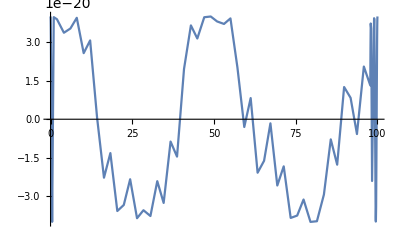

```mathematica
Plot[momentum[τ],{τ,0,100}]
```